# Conditions for Best-Response Relations using Expected SARSA

The function below calculates the best-responses that are possible given an opponents strategy. The output gives the best-response possibilities together with the conditions on the model parameters for their existence.

```mathematica
result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
With[{r=1, p=0},Do[{
strat = str[[j]];
assumptions = {
               If[strat[[1]]==0, q111>q112, q111<q112],
               If[strat[[2]]==0, q121>q122, q121<q122],
               If[strat[[3]]==0, q131>q132, q131<q132],
               If[strat[[4]]==0, q141>q142, q141<q142],
               If[input[[1]]==0, q211>q212, q211<q212],
               If[input[[2]]==0, q231>q232, q231<q232],
               If[input[[3]]==0, q221>q222, q221<q222],
               If[input[[4]]==0, q241>q242, q241<q242],
               ,t>r>p>s,2r>t+s, 0<delta<1, 0<epsilon<1};

Assuming[assumptions,
{eq11 = Simplify[q111==(1-epsilon/2)(Boole[q211>q212](p+delta ((1-epsilon/2)q111+(epsilon/2)q112) Boole[q111>q112] + delta ((epsilon/2)q111+(1-epsilon/2)q112) Boole[q111<q112])+Boole[q211<q212](t+delta ((1-epsilon/2)q121+(epsilon/2)q122) Boole[q121>q122] + delta ((epsilon/2)q121+(1-epsilon/2)q122) Boole[q121<q122]))+(epsilon/2)(Boole[q211<q212](p+delta ((1-epsilon/2)q111+(epsilon/2)q112) Boole[q111>q112] + delta ((epsilon/2)q111+(1-epsilon/2)q112) Boole[q111<q112])+Boole[q211>q212](t+delta ((1-epsilon/2)q121+(epsilon/2)q122) Boole[q121>q122] + delta ((epsilon/2)q121+(1-epsilon/2)q122) Boole[q121<q122]))];
eq12 = Simplify[q112==(1-epsilon/2)(Boole[q211>q212](s+delta ((1-epsilon/2)q131+(epsilon/2)q132) Boole[q131>q132] + delta ((epsilon/2)q131+(1-epsilon/2)q132) Boole[q131<q132])+Boole[q211<q212](r+delta ((1-epsilon/2)q141+(epsilon/2)q142) Boole[q141>q142] + delta ((epsilon/2)q141+(1-epsilon/2)q142)Boole[q141<q142]))+(epsilon/2)(Boole[q211<q212](s+delta ((1-epsilon/2)q131+(epsilon/2)q132) Boole[q131>q132] + delta ((epsilon/2)q131+(1-epsilon/2)q132) Boole[q131<q132])+Boole[q211>q212](r+delta ((1-epsilon/2)q141+(epsilon/2)q142) Boole[q141>q142] + delta ((epsilon/2)q141+(1-epsilon/2)q142)Boole[q141<q142]))];
eq13 = Simplify[q121==(1-epsilon/2)(Boole[q221>q222](p+delta ((1-epsilon/2)q111+(epsilon/2)q112) Boole[q111>q112] + delta ((epsilon/2)q111+(1-epsilon/2)q112) Boole[q111<q112])+Boole[q221<q222](t+delta ((1-epsilon/2)q121+(epsilon/2)q122) Boole[q121>q122] + delta ((epsilon/2)q121+(1-epsilon/2)q122) Boole[q121<q122]))+(epsilon/2)(Boole[q221<q222](p+delta ((1-epsilon/2)q111+(epsilon/2)q112) Boole[q111>q112] + delta ((epsilon/2)q111+(1-epsilon/2)q112) Boole[q111<q112])+Boole[q221>q222](t+delta ((1-epsilon/2)q121+(epsilon/2)q122) Boole[q121>q122] + delta ((epsilon/2)q121+(1-epsilon/2)q122) Boole[q121<q122]))];
eq14 = Simplify[q122==(1-epsilon/2)(Boole[q221>q222](s+delta ((1-epsilon/2)q131+(epsilon/2)q132) Boole[q131>q132] + delta ((epsilon/2)q131+(1-epsilon/2)q132) Boole[q131<q132])+Boole[q221<q222](r+delta ((1-epsilon/2)q141+(epsilon/2)q142) Boole[q141>q142] + delta ((epsilon/2)q141+(1-epsilon/2)q142)Boole[q141<q142]))+(epsilon/2)(Boole[q221<q222](s+delta ((1-epsilon/2)q131+(epsilon/2)q132) Boole[q131>q132] + delta ((epsilon/2)q131+(1-epsilon/2)q132) Boole[q131<q132])+Boole[q221>q222](r+delta ((1-epsilon/2)q141+(epsilon/2)q142) Boole[q141>q142] + delta ((epsilon/2)q141+(1-epsilon/2)q142)Boole[q141<q142]))];
eq15 = Simplify[q131==(1-epsilon/2)(Boole[q231>q232](p+delta ((1-epsilon/2)q111+(epsilon/2)q112) Boole[q111>q112] + delta ((epsilon/2)q111+(1-epsilon/2)q112) Boole[q111<q112])+Boole[q231<q232](t+delta ((1-epsilon/2)q121+(epsilon/2)q122) Boole[q121>q122] + delta ((epsilon/2)q121+(1-epsilon/2)q122) Boole[q121<q122]))+(epsilon/2)(Boole[q231<q232](p+delta ((1-epsilon/2)q111+(epsilon/2)q112) Boole[q111>q112] + delta ((epsilon/2)q111+(1-epsilon/2)q112) Boole[q111<q112])+Boole[q231>q232](t+delta ((1-epsilon/2)q121+(epsilon/2)q122) Boole[q121>q122] + delta ((epsilon/2)q121+(1-epsilon/2)q122) Boole[q121<q122]))];
eq16 = Simplify[q132==(1-epsilon/2)(Boole[q231>q232](s+delta ((1-epsilon/2)q131+(epsilon/2)q132) Boole[q131>q132] + delta ((epsilon/2)q131+(1-epsilon/2)q132) Boole[q131<q132])+Boole[q231<q232](r+delta ((1-epsilon/2)q141+(epsilon/2)q142) Boole[q141>q142] + delta ((epsilon/2)q141+(1-epsilon/2)q142)Boole[q141<q142]))+(epsilon/2)(Boole[q231<q232](s+delta ((1-epsilon/2)q131+(epsilon/2)q132) Boole[q131>q132] + delta ((epsilon/2)q131+(1-epsilon/2)q132) Boole[q131<q132])+Boole[q231>q232](r+delta ((1-epsilon/2)q141+(epsilon/2)q142) Boole[q141>q142] + delta ((epsilon/2)q141+(1-epsilon/2)q142)Boole[q141<q142]))];
eq17 = Simplify[q141==(1-epsilon/2)(Boole[q241>q242](p+delta ((1-epsilon/2)q111+(epsilon/2)q112) Boole[q111>q112] + delta ((epsilon/2)q111+(1-epsilon/2)q112) Boole[q111<q112])+Boole[q241<q242](t+delta ((1-epsilon/2)q121+(epsilon/2)q122) Boole[q121>q122] + delta ((epsilon/2)q121+(1-epsilon/2)q122) Boole[q121<q122]))+(epsilon/2)(Boole[q241<q242](p+delta ((1-epsilon/2)q111+(epsilon/2)q112) Boole[q111>q112] + delta ((epsilon/2)q111+(1-epsilon/2)q112) Boole[q111<q112])+Boole[q241>q242](t+delta ((1-epsilon/2)q121+(epsilon/2)q122) Boole[q121>q122] + delta ((epsilon/2)q121+(1-epsilon/2)q122) Boole[q121<q122]))];
eq18 = Simplify[q142==(1-epsilon/2)(Boole[q241>q242](s+delta ((1-epsilon/2)q131+(epsilon/2)q132) Boole[q131>q132] + delta ((epsilon/2)q131+(1-epsilon/2)q132) Boole[q131<q132])+Boole[q241<q242](r+delta ((1-epsilon/2)q141+(epsilon/2)q142) Boole[q141>q142] + delta ((epsilon/2)q141+(1-epsilon/2)q142)Boole[q141<q142]))+(epsilon/2)(Boole[q241<q242](s+delta ((1-epsilon/2)q131+(epsilon/2)q132) Boole[q131>q132] + delta ((epsilon/2)q131+(1-epsilon/2)q132) Boole[q131<q132])+Boole[q241>q242](r+delta ((1-epsilon/2)q141+(epsilon/2)q142) Boole[q141>q142] + delta ((epsilon/2)q141+(1-epsilon/2)q142)Boole[q141<q142]))];}];
sol1=Solve[{eq11, eq12, eq13, eq14, eq15, eq16, eq17, eq18}, {q111, q112, q121, q122, q131, q132, q141, q142}];
conditions1=Simplify[Assuming[assumptions,{Simplify[If[strat[[1]]==0,sol1[[1]][[1]][[2]]>sol1[[1]][[2]][[2]],sol1[[1]][[1]][[2]]<sol1[[1]][[2]][[2]]]] ,If[strat[[2]]==0,sol1[[1]][[3]][[2]]>sol1[[1]][[4]][[2]], sol1[[1]][[3]][[2]]<sol1[[1]][[4]][[2]]],If[strat[[3]]==0,sol1[[1]][[5]][[2]]>sol1[[1]][[6]][[2]], sol1[[1]][[5]][[2]]<sol1[[1]][[6]][[2]]], If[strat[[4]]==0,sol1[[1]][[7]][[2]]>sol1[[1]][[8]][[2]],sol1[[1]][[7]][[2]]<sol1[[1]][[8]][[2]]]}]];
possiblebase=Simplify[conditions1[[1]]&&conditions1[[2]]&&conditions1[[3]]&&conditions1[[4]]];
possiblebase1=Assuming[{assumptions},Simplify[Reduce[possiblebase&&t>r&&t>p&&t>s&&r>p&&r>s&&p>s&&0<delta&&1>delta&&0<epsilon&&1>epsilon&&s+t<2r]]];
If[possiblebase1 , AppendTo[output,{FromDigits[i,2]+1->j,True}],,possible = Assuming[{assumptions},Simplify[conditions1[[1]]&&conditions1[[2]]&&conditions1[[3]]&&conditions1[[4]]]];
If[(possible === 0)==False , AppendTo[output,{FromDigits[i,2]+1->j,Simplify[possible]}]]];
},{j,1,16}]];
output
];
```

```mathematica
strats = {};
Do[AppendTo[strats, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];
```

Providing an index i for the strats function in the code below produces the possible best-response relationships given that an opponent uses strategy i.

```mathematica
Simplify[result[strats[[14]], strats]]
```

{{14→1,2+delta (2-3 epsilon+epsilon^2)+epsilon (-1+s+t)<2 t&&(1+delta) epsilon+2 (1+delta) s+2 delta epsilon^2 s<epsilon (s+delta (epsilon+4 s)+t)},{14→12,2 (-1+t)<delta (2-3 epsilon+epsilon^2)+epsilon (-1+s+t)&&epsilon (-1+delta (-1+epsilon)+s+t)>2 s},{14→16,delta (-1+epsilon) (2-2 s+epsilon (-1+2 s))+2 (-1+t)<epsilon (-1+s+t)&&epsilon (delta epsilon+s+t)<epsilon+delta epsilon+2 s}}

## Transition conditions in the iterated prisoner’s dilemma

Below we collect the possible best-response relations together with their conditions for the iterated prisoner’s dilemma.

```mathematica
transitionsIPD ={
{1->1,True}, 
{2->1,2+2 delta t+epsilon (s+t)+delta epsilon^2 (s+t)<epsilon+2 t+delta epsilon (s+3 t)&&epsilon+2 s+delta epsilon^2 s+delta epsilon t<epsilon (s+delta s+t+delta epsilon t)},{2->2,2+2 (-1+delta) t+delta epsilon^2 (s+t)+epsilon (-1+s-delta s+t-3 delta t)>0&&2 (-1+delta) s+delta epsilon^2 (s+t)+epsilon (-1+s-3 delta s+t-delta t)>0},{2->16,delta (2+epsilon^2) s+delta epsilon^2 t+epsilon (s+t)<epsilon+2 s+delta epsilon (3 s+t)&&epsilon+delta epsilon^2 s+3 delta epsilon t+2 (delta s+t)<2+2 delta t+delta epsilon^2 t+epsilon (s+3 delta s+t)}, 
{3->1,True}, 
{4->1,True},
{5->1,2+epsilon (-1+delta+s+t)<delta epsilon^2+2 t&&epsilon (-1+s+t+delta (-1+epsilon+4 t-2 epsilon t))>2 (s+delta t)},{5->14,2+epsilon (-1+s+t)<2 t+delta (-1+epsilon) (2-2 t+epsilon (-1+2 t))&&epsilon (-1+s+t+delta (-1+epsilon+4 t-2 epsilon t))<2 (s+delta t)},{5->16,epsilon+delta (2+epsilon^2)+2 s>epsilon (3 delta+s+t)&&2 (-1+t)+delta (-1+epsilon) (2-2 t+epsilon (-1+2 t))<epsilon (-1+s+t)},
{6->1,epsilon (1-s-t+delta (-1+s+3 t))>2+2 (-1+delta) t+delta epsilon^2 (-1+s+t)&&epsilon (-1+s+t+delta (-1+s+3 t))>delta epsilon^2 (-1+s+t)+2 (s+delta t)},{6->4,epsilon (-1+s+t)+delta (-1+epsilon) (2-2 s+epsilon (-1+s+t))>2 s&&2+2 (-1+delta) t+delta epsilon^2 (-1+s+t)+epsilon (-1+s+t-delta (-1+s+3 t))>0},{6->13,2+epsilon (-1+s+t)<2 t+delta (-1+epsilon) (2-2 s+epsilon (-1+s+t))&&epsilon (-1+s+t+delta (-1+s+3 t))<delta epsilon^2 (-1+s+t)+2 (s+delta t)},{6->16,2 (-1+t)+delta (-1+epsilon) (2-2 s+epsilon (-1+s+t))<epsilon (-1+s+t)&&epsilon (-1+s+t)+delta (-1+epsilon) (2-2 s+epsilon (-1+s+t))<2 s},
{7->1,2 (-1+delta) s+2 delta epsilon^2 (s-t)+epsilon (-1+s-4 delta s+t+4 delta t)>2 delta t},{7->10,2 (-1+delta) s+2 delta epsilon^2 (s-t)+epsilon (-1+s-4 delta s+t+4 delta t)<2 delta t},
{8->1,2 (-1+delta) s+delta epsilon^2 (s-t)+epsilon (-1+s-3 delta s+t+3 delta t)>2 delta t&&2 (-1+t)>epsilon (-1+s+t)+delta (-1+epsilon) (2-2 t+epsilon (-2+s+t))},{8->9,2 (-1+delta) s+delta epsilon^2 (s-t)+epsilon (-1+s-3 delta s+t+3 delta t)<2 delta t&&epsilon+(-1+delta) epsilon s+2 (-1+t)+delta epsilon^2 (-s+t)>(1+delta) epsilon t},{8->16,epsilon (-1+s+t)+delta (-1+epsilon) (2-2 s+epsilon (-2+s+t))<2 s&&2+delta epsilon^2 (s-t)+epsilon (-1+s-delta s+t+delta t)>2 t},
{9->1,True},
{10->1,2+2 delta (-1+epsilon)^2+epsilon (-1+s+t)<2 t},
{10->10,2 (-1+t)<2 delta (-1+epsilon)^2+epsilon (-1+s+t)},
{11->1,True},
{12->1,True},
{13->1,True},
{14->1,2+delta (2-3 epsilon+epsilon^2)+epsilon (-1+s+t)<2 t&&(1+delta) epsilon+2 (1+delta) s+2 delta epsilon^2 s<epsilon (s+delta (epsilon+4 s)+t)},{14->12,2 (-1+t)<delta (2-3 epsilon+epsilon^2)+epsilon (-1+s+t)&&epsilon (-1+delta (-1+epsilon)+s+t)>2 s},{14->16,delta (-1+epsilon) (2-2 s+epsilon (-1+2 s))+2 (-1+t)<epsilon (-1+s+t)&&epsilon (delta epsilon+s+t)<epsilon+delta epsilon+2 s},
{15->1,True},
{16->1,True}};
```

#### Possible absorbing states

By examining the possible best-response relations we see that the only absorbing strategy pairs are strategies 1, 2 and 10. These correspond to the all defect (All-D), grim trigger (GT) and win-stay, lose, shift (WSLS) strategies respectively.

#### Basin of attraction of WSLS strategy pair

The WSLS strategy is a best-response to itself when  2 (-1+t)<2 delta (-1+epsilon)^2+epsilon (-1+s+t). When this condition holds, the WSLS strategy pair is an absorbing state under mutual best-response dynamics.  By examining the possible transitions, we see that only strategy 7 and 10 can be in the basin of attraction of the WSLS strategy pair. This translates into a maximum of four strategy pairs in the mutual best-response graph and since there are a total of 256 strategy pairs the basin of attraction of the WSLS strategy pair has a maximum of approximately 1.6 percent.

## Plotting the best-response graph

With the code below we can plot the best-response graph given a choice of model parameters.

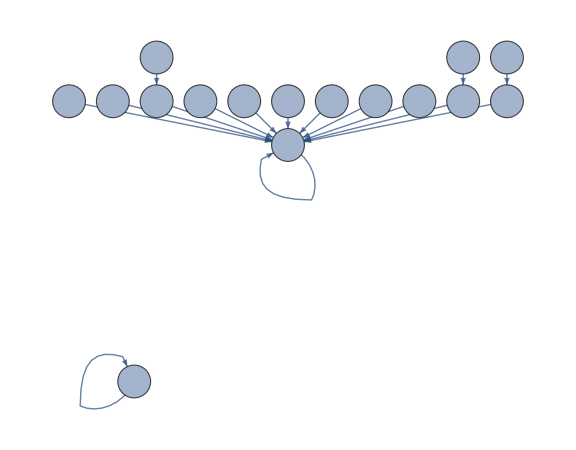

```mathematica
edgesSimple = {};
Do[If[Reduce[transitionsIPD[[j]][[2]]/.{t->1.2,s->-0.05, epsilon->0.68 ,delta->0.7}]==True,AppendTo[edgesSimple,transitionsIPD[[j]][[1]]]],{j,1,Length[transitionsIPD]}];
Graph[edgesSimple, VertexLabels->Placed[Automatic,Center],VertexSize->.75, ImageSize->Large]
```